```mathematica
Tip[i_,n_]:=If[EvenQ[i],
Join[Table[2*i*If[OddQ[k], 1, 0], {k, 0, i-1}], ConstantArray[0, n-i]], Join[Table[i*(If[k==0, 1, 0]+2*If[And[EvenQ[k], k>0], 1, 0]), {k, 0, i-1}], ConstantArray[0, n-i]]];
Der[n_]:=Transpose[Table[Tip[i, n], {i, 0,n-1}]]
CzybPoints[n_]:=Table[Cos[(π i)/(n-1)], {i, 0, n-1}];
CzybWeights[n_]:=Table[If[Or[i==0, i==n-1], π/(2(n-1)), π/(n-1)], {i, 0, n-1}];
CzybyszewGaussLobato[f_,n_]:=Table[
Sum[N[ChebyshevT[j, CzybPoints[n+1][[k+1]]]*f[CzybPoints[n+1][[k+1]]]*CzybWeights[n+1][[k+1]]],{k, 0, n}]/Sum[N[ChebyshevT[j, CzybPoints[n+1][[k+1]]]^2*CzybWeights[n+1][[k+1]]],{k, 0, n}], {j, 0, n-1}];
L[n_]:=Der[n].Der[n]-4*Der[n]+4IdentityMatrix[n];
BoundryMinus[n_]:=Table[ChebyshevT[i, -1], {i, 0, n-1}];
BoundryPlus[n_]:=Table[ChebyshevT[i, 1], {i, 0, n-1}];
Lbndr[n_]:=Join[Table[L[n][[i]], {i, 1, n-2}],{BoundryPlus[n], BoundryMinus[n]}];
S=(Exp[#1]+(-4 ⅇ)/(1+ⅇ^2)&);
Soln[n_, sol_]:=(Sum[sol[[i]]*ChebyshevT[i-1, #], {i, 1, n}]&);
BCzybyszewGaussLobato[f_,n_]:=Join[CzybyszewGaussLobato[f,n][[1;;n-2]], {0,0}];
CzybyszewNorms[i_]:=If[i==0, π, π/2];
```

#### Analytic solution below

```mathematica
fanal[x_]:=Exp[x]-Sinh[1]/Sinh[2] Exp[2x]+(- ⅇ)/(1+ⅇ^2);
```

#### Solution Here. Very nonoptimal but meh ...

```mathematica
sol4=Inverse[Lbndr[4]].BCzybyszewGaussLobato[S, 4]//N;
f4=Soln[4, sol4];
Inverse[Lbndr[8]].BCzybyszewGaussLobato[S, 8]//N;
f8=Soln[8, %];
Inverse[Lbndr[10]].BCzybyszewGaussLobato[S, 10]//N;
f10=Soln[10, %];
```

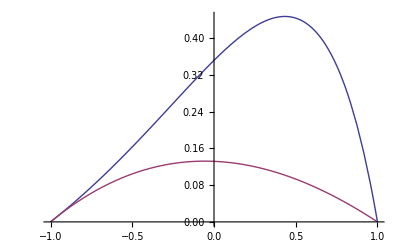

```mathematica
Plot[{fanal[x], f4[x]}, {x, -1, 1}]
```

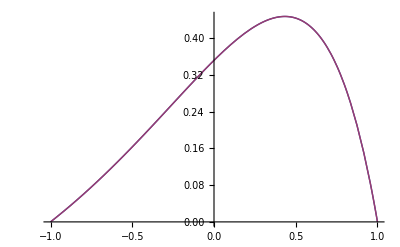

```mathematica
Plot[{fanal[x], f10[x]}, {x, -1, 1}]
```

```mathematica
BCzybyszewGaussLobato[S, 5]//MatrixForm//N
```

(-0.0300425
1.13032
0.27154
0.
0.)

```mathematica
Lbndr[4].sol4-BCzybyszewGaussLobato[S, 4]//N
```

{-2.08167×10^-17,0.,-1.73472×10^-18,-5.20417×10^-18}

```mathematica
Lbndr[6]//MatrixForm
```

(4 | -4 | 4 | -12 | 32 | -20
0 | 4 | -16 | 24 | -32 | 120
0 | 0 | 4 | -24 | 48 | -40
0 | 0 | 0 | 4 | -32 | 80
1 | 1 | 1 | 1 | 1 | 1
1 | -1 | 1 | -1 | 1 | -1)

```mathematica
SolDeg=Table[Soln[n, N[Inverse[L[n]].CzybyszewGaussLobato[S, n]]], {n, 4, 25}];
```

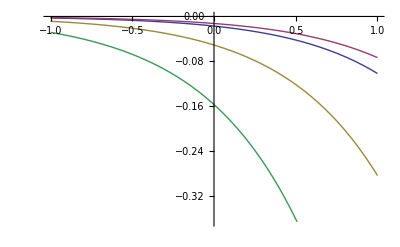

```mathematica
Plot[{SolDeg[[5]][x]-SolDeg[[10]][x],SolDeg[[5]][x]-SolDeg[[7]][x],SolDeg[[3]][x]-SolDeg[[7]][x],SolDeg[[1]][x]-SolDeg[[7]][x]}, {x, -1, 1}]
```

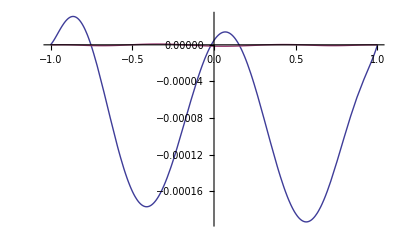

```mathematica
Plot[{f8[x]-fanal[x], f10[x]-fanal[x]}, {x, -1, 1}]
```

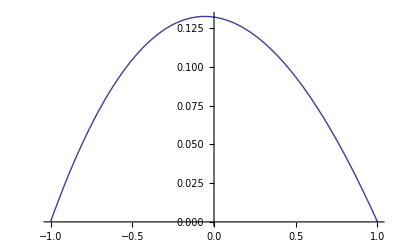
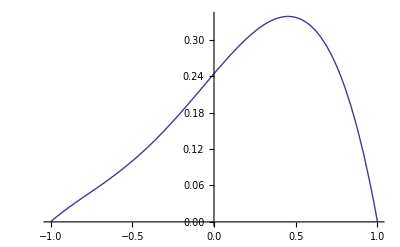
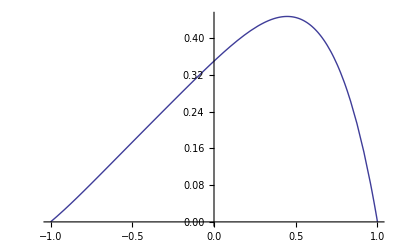
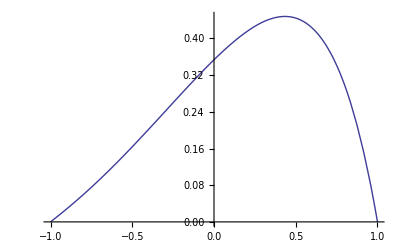
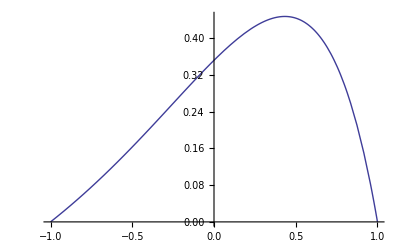
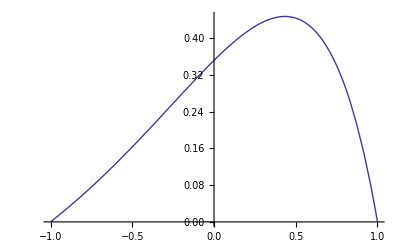
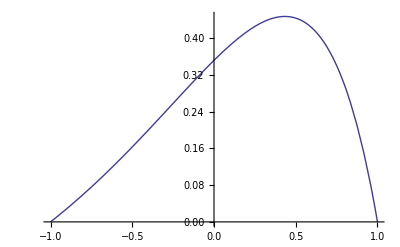

```mathematica
SolDeg
```

```mathematica
CzybyszewGaussLobato[S,8]-Table[NIntegrate[ChebyshevT[i, x]S[x]/Sqrt[1-x^2], {x, -1, 1}]/NIntegrate[ChebyshevT[i, x]^2/Sqrt[1-x^2], {x, -1, 1}], {i, 0, 7}]
```

{-1.47798×10^-15,2.19824×10^-14,-1.11022×10^-15,2.84911×10^-14,1.03673×10^-12,2.49673×10^-11,5.50588×10^-10,1.10368×10^-8}

#### The Galerkin Method

```mathematica
M[n_] :=Table[If[OddQ[j], -KroneckerDelta[i, 1], -KroneckerDelta[i, 2]]+KroneckerDelta[j+2, i],{i, 1, n}, {j, 1, n-2}] ;
```

```mathematica
GalerkinA[n_]:=Transpose[M[n]].L[n].DiagonalMatrix[Table[CzybyszewNorms[i], {i, 0, n-1}]].M[n]
```

```mathematica
GalerkinS[n_]:=CzybyszewGaussLobato[S, n].DiagonalMatrix[Table[CzybyszewNorms[i], {i, 0, n-1}]].M[n]
```

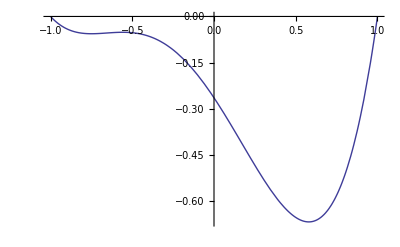

```mathematica
g5=Inverse[GalerkinA[5]].GalerkinS[5];
Plot[Soln[5, M[5].g5][x],{x, -1, 1}]
```

```mathematica
GalerkinA[5]//MatrixForm
GalerkinS[5]
DiagonalMatrix[Table[CzybyszewNorms[i], {i, 0, 5-1}]]//MatrixForm
```

(4 π | -8 π | 12 π
8 π | -8 π | 0
2 π | 4 π | -10 π)

{0.520846,-1.70585,0.103051}

(π | 0 | 0 | 0 | 0
0 | π/2 | 0 | 0 | 0
0 | 0 | π/2 | 0 | 0
0 | 0 | 0 | π/2 | 0
0 | 0 | 0 | 0 | π/2)